```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

```mathematica
<<NDSolve`FEM`
```

## Importing data

```mathematica
(*numerical solution, flag == 0,
 exact solution, flag == 1 and 
error flag == 2
error velocity space flag == 3
fe index distribution flag == 4
convergence table flag == 5*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["../",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 3,
filename=StringJoin["../",outputdir,"/solution/error_velocity_space",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 4,
filename=StringJoin["../",outputdir,"/solution/fe_index",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 5,
filename=StringJoin["../",outputdir,"/convergence_tables/convergence_table",refinetype,"degree_",ToString[p]]
];

Print[Style["Reading Data from...",FontColor->Black]];
Print[Style[ToString[filename],FontColor->Green]];
result = Import[filename,"Table"]⟦2;;-1,All⟧
]
```

## Solution

### G26 A

```mathematica
ndof=3840;
foldername = "/Tests/build/output_N3_heated_cylinder_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
```

Reading Data from...

..//Tests/build/output_N3_heated_cylinder_Kn0p1/solution/numerical_solution_global_degree_1_DOF_3840

```mathematica
ListPlot3D[numsol⟦All,{1,2,3}⟧]
```

ListPlot3D[$Failed⟦2;;-1,All⟧⟦All,{1,2,3}⟧]

## IDs for different variables

```mathematica
(*we declare the IDs for different variables, this will help us with plotting*)
IDRho = 1+2;
IDvx = 2+2;
IDvy = 3+2;
IDtheta = 4+2;
IDsigmaxx = 5+2;
IDsigmaxy = 6+2;
IDsigmayy = 7+2;
IDqx = 8+2;
IDqy = 9+2;
```

## Mapping to Primitive variables

```mathematica
(*we change the numerical solution obtained to the primitive variables.*)
ConvToPrim[sol_]:=Module[{factorθ,factorσ,factorq,trialsol},
trialsol = sol;
factorθ = -√(2/3);
factorσ = √2;
factorq = -√(5/2);
trialsol⟦All,IDtheta⟧ =factorθ * sol⟦All,IDtheta⟧;
trialsol⟦All,{IDqx,IDqy}⟧ =factorq*sol⟦All,{IDqx,IDqy}⟧;
trialsol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmayy}⟧=factorσ*sol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmayy}⟧;

trialsol
]
```

## Plotting help

### Reading the mesh

```mathematica
(*In the following function we read the gmsh file*)
ReadMeshFile[filename_]:=Import[filename,"Table"];

(*In the following function we extract the coordinates for the vertices*)
ExtractVertices[mesh_]:=Module[{nVerts,verts,offset},
(*offset from the gmsh *)
offset = 5;

(*total number of vertices in the mesh*)
nVerts = mesh⟦offset⟧⟦1⟧;

(*vertices of the mesh*)
verts = mesh⟦offset+1;;offset+nVerts,All⟧;

(*now we only extract the coordinates*)
verts⟦All,2;;-1⟧
]

(*In the following function we extract the elements*)
ExtractElements[mesh_]:=Module[{nElm,Elm,beginElm,beginQuads,offset},
(*location where the elements begin*)
beginElm = Position[mesh,"$Elements"]⟦1,1⟧;

(*Extract all the elements. This includes the physical groups which were defined during the mesh generation*)
Elm=mesh⟦beginElm;;-1,All⟧;

(*location where the actual quads begin, 3 because of the offset and 4 because that stores the ID of the physical entity.
The value 3 in the checks whether we have a quad or not.
*)
offset = 3;
Do[If[Length[Elm⟦ii⟧]≥5,If[Elm⟦ii⟧⟦2⟧==3,beginQuads=ii; Break[];Print["Inside"];]],{ii,1,Length[Elm]}];

(*from begin quads to -2 because the last element in $EndElements*)
Elm = Elm⟦beginQuads;;-2,6;;-1⟧;

Elm
]

(*In the following routine we check the mesh which we have read from the file*)
CheckElms[Elms_,nVerts_]:=Module[{},

(*We check whether all the vertices have been included or not in the connectivity data*)

If[Norm[DeleteDuplicates[Sort[Flatten[Elms]]]-Range[1,nVerts]]==0,Print[Style["Correct Mesh",FontColor->Green]],Print[Style["InCorrect Mesh",FontColor->Red]]]
];


CreateMesh[mesh_,dim_]:=Module[{Verts,Elms,OrderedVerts,nVerts,finalMesh},

Verts = ExtractVertices[mesh]⟦All,1;;dim⟧;
nVerts = Length[Verts];
Elms = ExtractElements[mesh];

CheckElms[Elms,nVerts];
finalMesh = ToElementMesh["Coordinates"->Verts,"MeshElements"->{QuadElement[Elms]},"MeshOrder"->3];

finalMesh
]
```

### Interpolation

```mathematica
InterpolateSolution[solution_]:=Module[{densityData,vxData,vyData,thetaData,sigmaxxData,sigmaxyData,sigmayyData,qxData,qyData,pressureData,densityValue},

(*convert data into a format which is read by Interpolation*)
densityData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDRho⟧},{ii,1,Length[solution]}];

vxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDvx⟧},{ii,1,Length[solution]}];

vyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDvy⟧},{ii,1,Length[solution]}];

thetaData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDtheta⟧},{ii,1,Length[solution]}];

(*sigmaxxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmaxx⟧},{ii,1,Length[solution]}];

sigmaxyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmaxy⟧},{ii,1,Length[solution]}];

sigmayyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmayy⟧},{ii,1,Length[solution]}];

qxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDqx⟧},{ii,1,Length[solution]}];

qyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDqy⟧},{ii,1,Length[solution]}];

pressureData=Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDtheta⟧+solution⟦ii,IDRho⟧},{ii,1,Length[solution]}];*)

(*remove the duplicate entries for Interpolation function*)
densityData = DeleteDuplicatesBy[densityData,First];
vxData = DeleteDuplicatesBy[vxData,First];
vyData = DeleteDuplicatesBy[vyData,First];
thetaData = DeleteDuplicatesBy[thetaData,First];
(*sigmaxxData = DeleteDuplicatesBy[sigmaxxData,First];
sigmaxyData = DeleteDuplicatesBy[sigmaxyData,First];
sigmayyData = DeleteDuplicatesBy[sigmayyData,First];
qxData = DeleteDuplicatesBy[qxData,First];
qyData = DeleteDuplicatesBy[qyData,First];
pressureData=DeleteDuplicatesBy[pressureData,First];*)

(*we first need to compute the value of the solution a the mesh points*)
(*densityData=Interpolation[densityData,InterpolationOrder->1];
densityValue = densityData[0,Sequence@@#]&/@coords;*)

densityData=Interpolation[densityData,InterpolationOrder->1];
vxData=Interpolation[vxData,InterpolationOrder->1];
vyData=Interpolation[vyData,InterpolationOrder->1];
thetaData=Interpolation[thetaData,InterpolationOrder->1];
(*sigmaxxData=Interpolation[sigmaxxData,InterpolationOrder->1];
sigmaxyData=Interpolation[sigmaxyData,InterpolationOrder->1];
sigmayyData=Interpolation[sigmayyData,InterpolationOrder->1];
qxData=Interpolation[qxData,InterpolationOrder->1];
qyData=Interpolation[qyData,InterpolationOrder->1];
pressureData=Interpolation[pressureData,InterpolationOrder->1];*)

{densityData,vxData,vyData,thetaData,sigmaxxData,sigmaxyData,sigmayyData,qxData,qyData,pressureData}
]
```

### Plot Contour

```mathematica
PlotContour[data_,domain_,ratio_,range_]:=Module[{label},

label={Style["x",FontSize->14],Style["y",FontSize->14],None,None};

ContourPlot[data,{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],ContourLines->False,Contours->10,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/ratio,ContourLabels->False,Frame->True,FrameTicksStyle->{16,16},FrameLabel->label,RotateLabel->False,Exclusions->None]

]
```

### Plot Streamlines

```mathematica
PlotStreamlines[data_,domain_,ratio_,range_]:=Module[{},
StreamPlot[{Sum[(data⟦ii,1⟧[x,y])/Length[data],{ii,1,Length[data]}],Sum[(data⟦ii,2⟧[x,y])/Length[data],{ii,1,Length[data]}]},{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],PlotRange->{Full,Full},PlotLegends->None,AspectRatio->1/ratio,StreamStyle->Green,StreamPoints->{Automatic,0.05},ImageSize->Large]]
```

### Plot Vector

```mathematica
PlotVectorlines[data_,domain_,ratio_,range_]:=Module[{},
VectorPlot[{Sum[(data⟦ii,1⟧[x,y])/Length[data],{ii,1,Length[data]}],Sum[(data⟦ii,2⟧[x,y])/Length[data],{ii,1,Length[data]}]},{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],PlotRange->{Full,Full},ColorFunction->Hue,PlotLegends->Automatic,AspectRatio->1/ratio,VectorPoints->30,ImageSize->Large,VectorScale->0.05]]
```

### Sort Solution

## Solution NACA5012(Full Accommodation)

### Create mesh

```mathematica
Data = ReadMeshFile["../Meshes/Channel_NACA5012/NACA5012_Channel_Cells_6363.msh"];
DomainMesh = CreateMesh[Data,2];
```

Correct Mesh

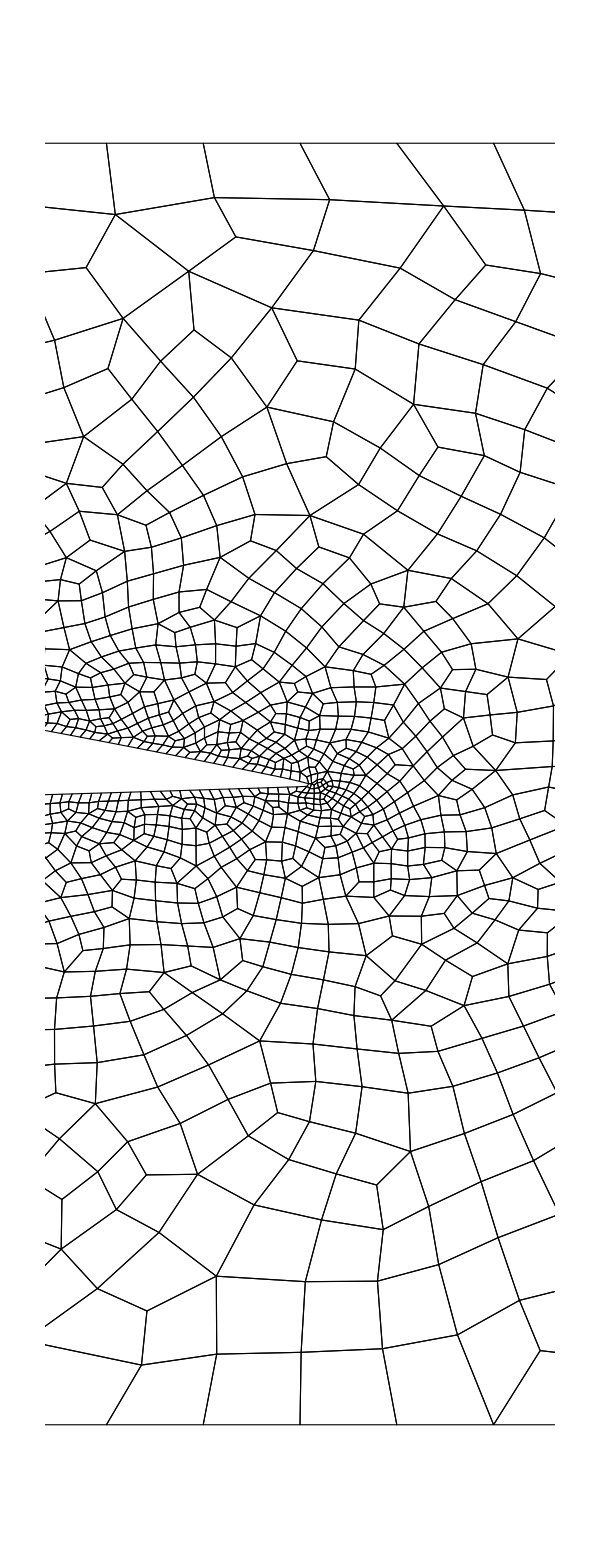

```mathematica
MeshPlot=DomainMesh["Wireframe"["MeshElementStyle"->EdgeForm[{Thin,Black}],PlotRange->{{0.9,1.1},All},ImageSize->600]]
```

### G35

```mathematica
ndof=559944;
foldername = "/Results/Results_NACA/output_G35_odd_NACA5012_Kn0p1";
numsol=importdata[ndof,1,"_global_",0,foldername];
numsol = ConvToPrim[numsol];
solution = InterpolateSolution[numsol,DomainMesh];
```

#### vx

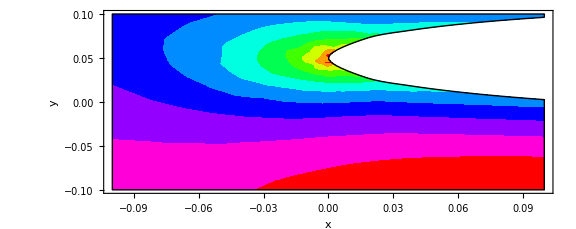

```mathematica
vxPlot=PlotContourRegionFunction[solution⟦IDvx-2⟧,MeshRegion[DomainMesh],2.5,{{-0.1,0.1},{-0.1,0.1}}]
```

#### vy

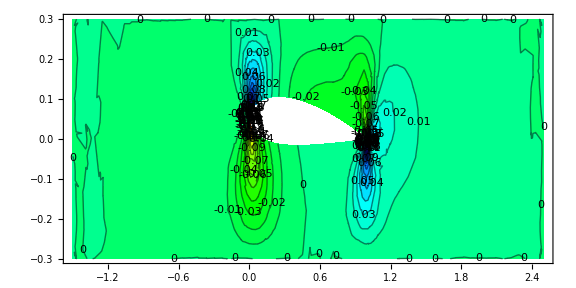

```mathematica
PlotContour[solution20⟦IDvy-2⟧,MeshRegion[DomainMesh],2]
```

#### θ

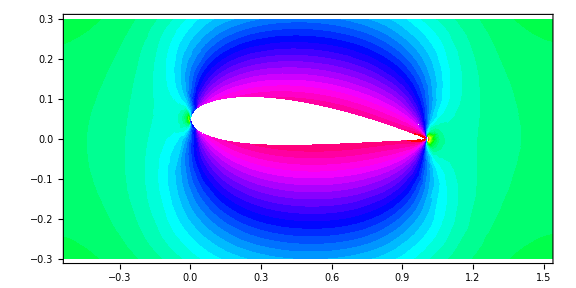

```mathematica
θPlot=PlotContour[solution⟦IDtheta-2⟧,MeshRegion[DomainMesh],2]
```

#### pressure

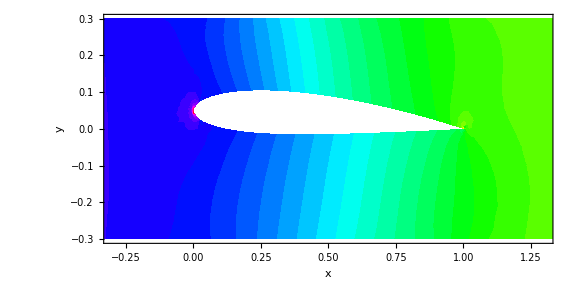

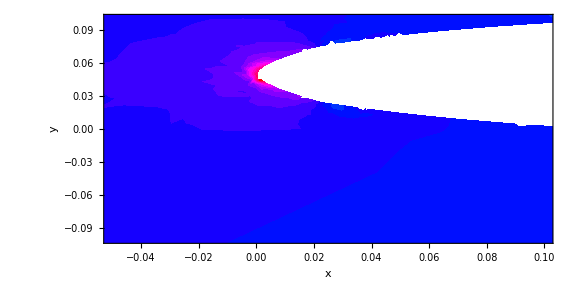

```mathematica
PressurePlot=PlotContour[solution⟦-1⟧,MeshRegion[DomainMesh],2,{{-0.3,1.3},Full}]
PressureZoom=PlotContour[solution⟦-1⟧,MeshRegion[DomainMesh],2,{{-0.05,0.1},{-0.1,0.1}}]
```

#### qx

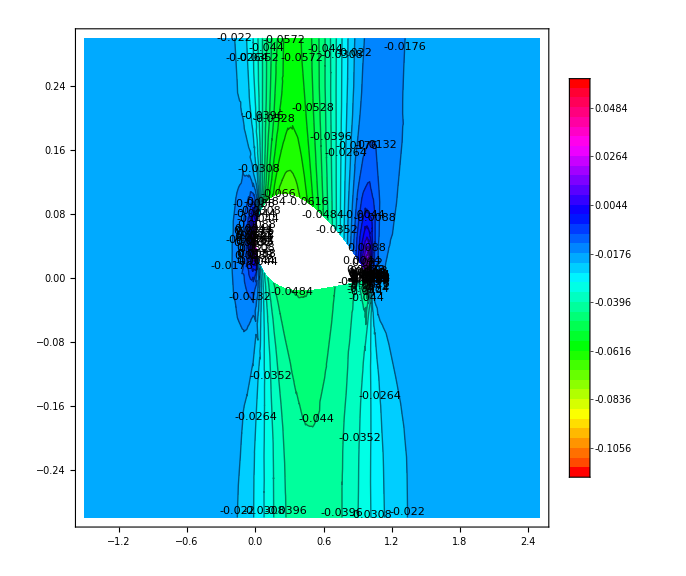

```mathematica
PlotContour[solution20⟦IDqx-2⟧,MeshRegion[DomainMesh],1]
```

#### qy

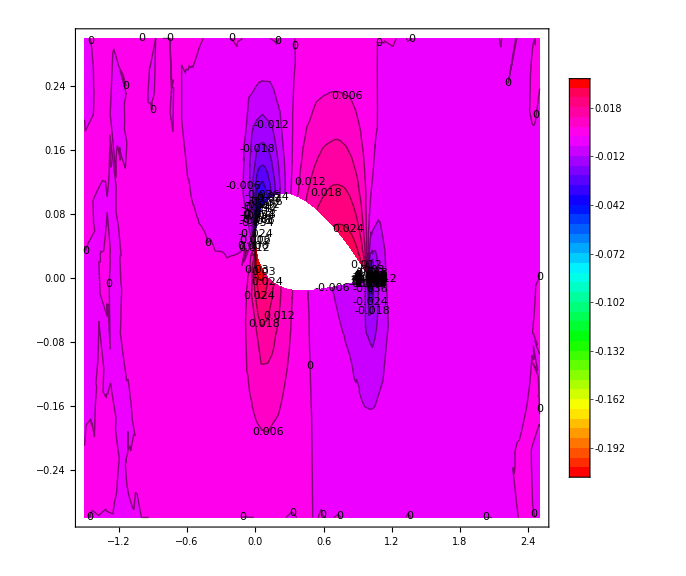

```mathematica
PlotContour[solution20⟦IDqy-2⟧,MeshRegion[DomainMesh],1]
```

#### sigmaxx

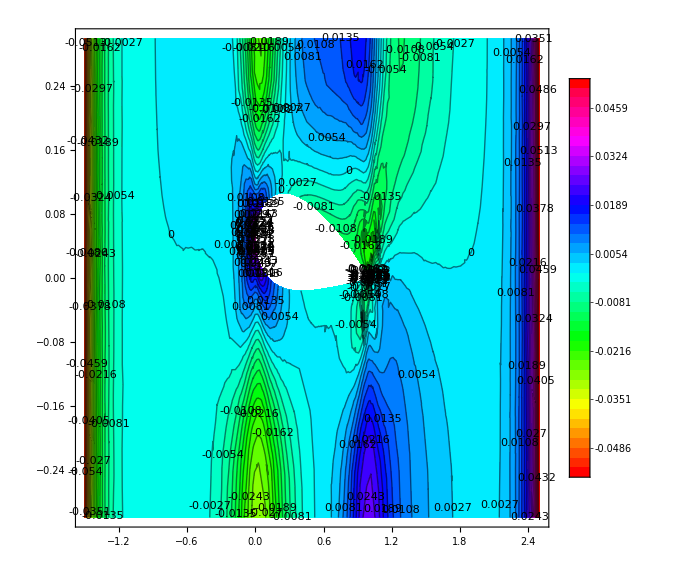

```mathematica
PlotContour[solution20⟦IDsigmaxx-2⟧,MeshRegion[DomainMesh],1]
```

#### sigmaxy

```mathematica
PlotContour[solution20⟦IDsigmaxy-2⟧,MeshRegion[NACA5012Mesh]]
```

PlotContour[InterpolatingFunction[{{-1.5, 2.5}, {-0.3, 0.3}}, <>],MeshRegion[NACA5012Mesh]]

#### sigmayy

```mathematica
PlotContour[solution20⟦IDsigmayy-2⟧,MeshRegion[NACA5012Mesh]]
```

PlotContour[InterpolatingFunction[{{-1.5, 2.5}, {-0.3, 0.3}}, <>],MeshRegion[NACA5012Mesh]]

#### Velocity field

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[vxPlot,PlotVectorlines[solution⟦{IDvx-2,IDvy-2}⟧,MeshRegion[DomainMesh],2.5]]
```

-Graphics-

## Solution Channel Rectangle

### Create mesh

```mathematica
Data = ReadMeshFile["../Meshes/Channel_Rectangle/rectangle.msh"];
DomainMesh = CreateMesh[Data,2];
```

Correct Mesh

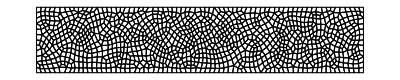

```mathematica
MeshPlot=DomainMesh["Wireframe"["MeshElementStyle"->EdgeForm[{Thin,Black}]]]
```

### G20

```mathematica
ndof=56732;
foldername = "Tests/build/output_G20_odd_channel_rectangle_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];
solution20 = InterpolateSolution[numsol20];
```

#### Rho

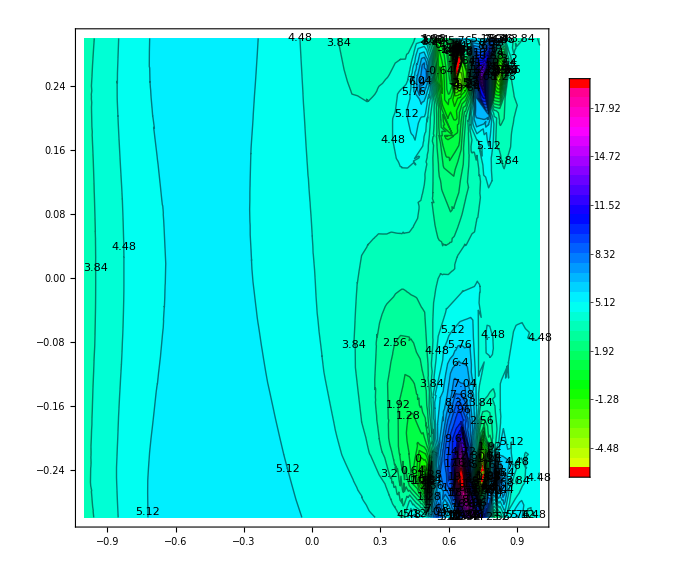

```mathematica
PlotContour[solution20⟦IDRho-2⟧,MeshRegion[DomainMesh],1]
```

#### vx

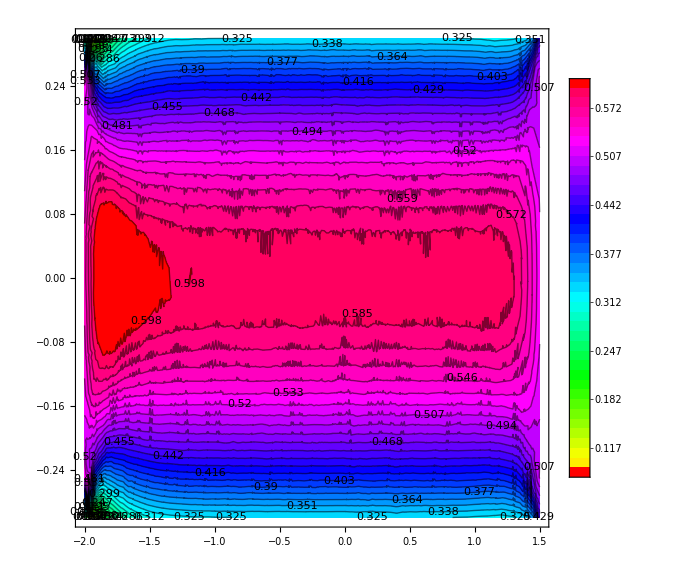

```mathematica
PlotContour[solution20⟦IDvx-2⟧,MeshRegion[DomainMesh],1]
```

#### vy

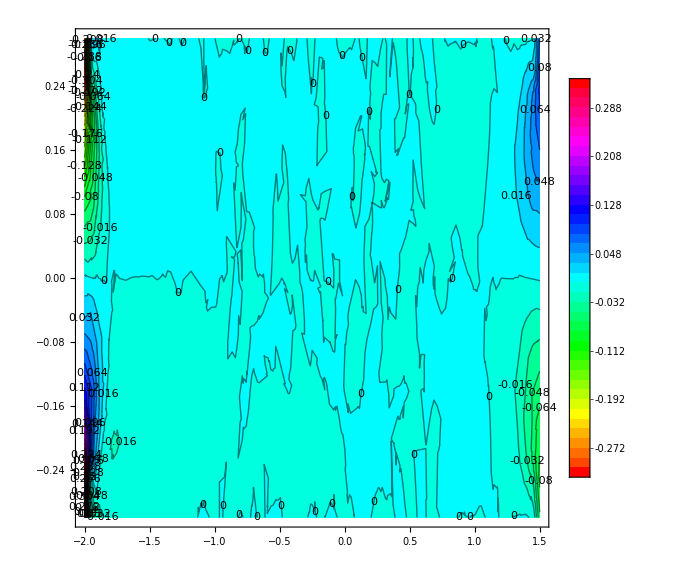

```mathematica
PlotContour[solution20⟦IDvy-2⟧,MeshRegion[DomainMesh],1]
```

#### θ

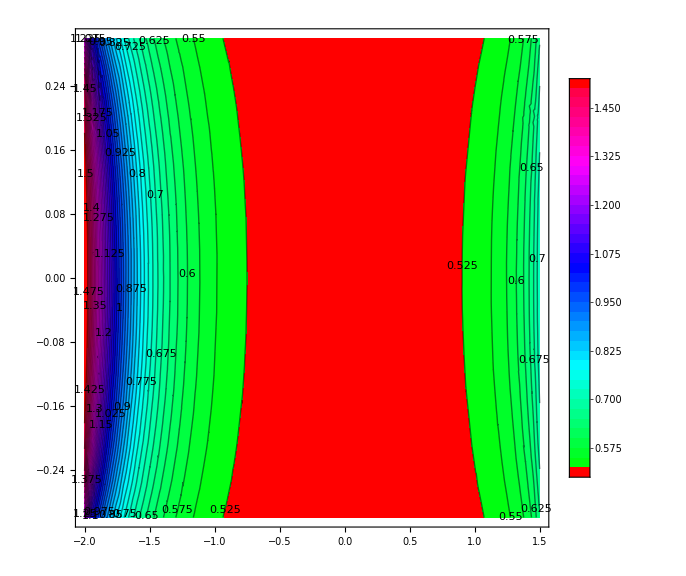

```mathematica
PlotContour[solution20⟦IDtheta-2⟧,MeshRegion[DomainMesh],1]
```

#### Pressure

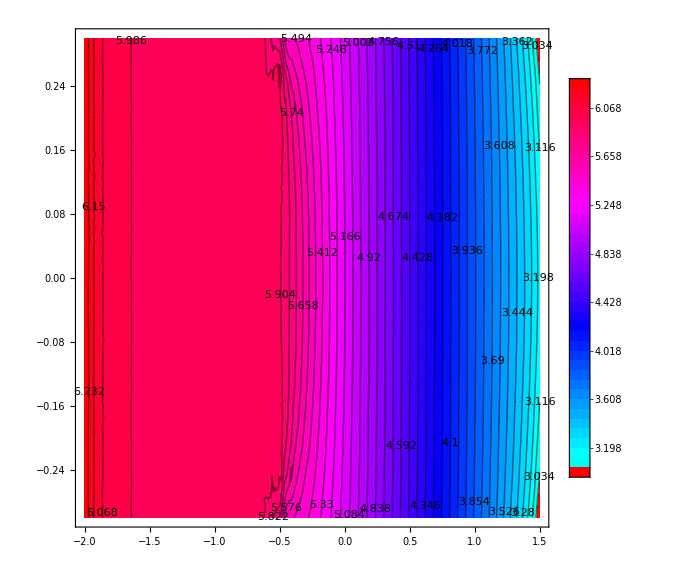

```mathematica
PlotContour[solution20⟦-1⟧,MeshRegion[DomainMesh],1]
```

#### qx

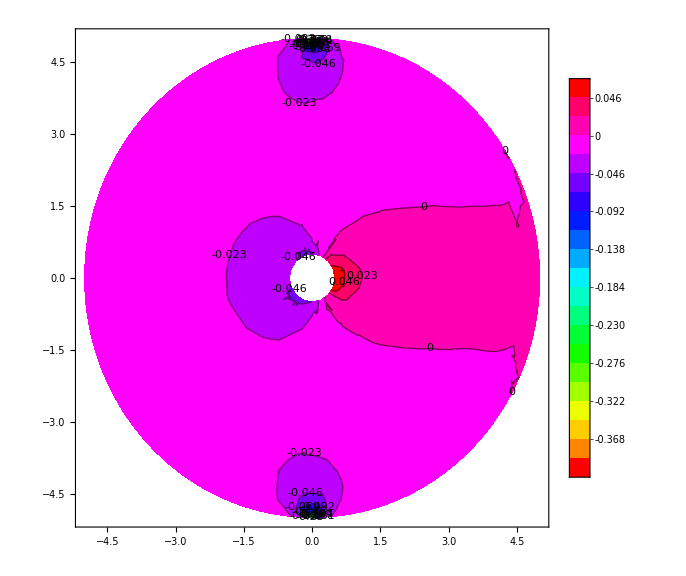

```mathematica
PlotContour[solution20⟦IDqx-2⟧,MeshRegion[DomainMesh],1]
```

#### qy

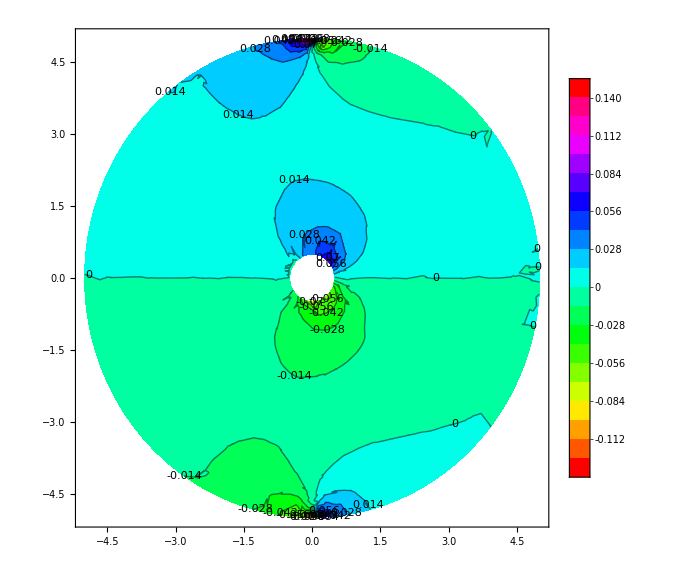

```mathematica
PlotContour[solution20⟦IDqy-2⟧,MeshRegion[DomainMesh],1]
```

#### sigmaxx

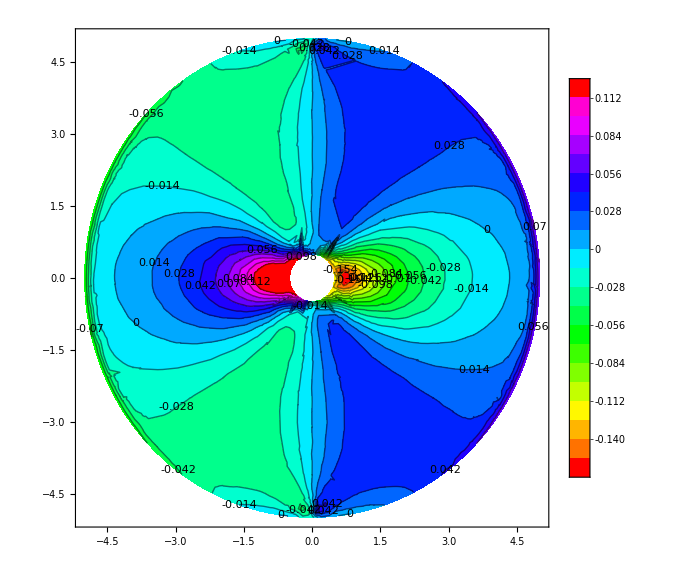

```mathematica
PlotContour[solution20⟦IDsigmaxx-2⟧,MeshRegion[DomainMesh],1]
```

#### sigmaxy

```mathematica
PlotContour[solution20⟦IDsigmaxy-2⟧,MeshRegion[mesh],1]
```

InterpolatingFunction::dmval: Input value {-0.146243,4.99713} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

#### sigmayy

```mathematica
PlotContour[solution20⟦IDsigmayy-2⟧,MeshRegion[mesh],1]
```

-Graphics-

#### Velocity field

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[PlotStreamlines[solution20⟦{IDvx-2,IDvy-2}⟧,MeshRegion[DomainMesh],1],MeshPlot]
```

-Graphics-

#### Heat flow filed

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[PlotStreamlines[solution20⟦{IDqx-2,IDqy-2}⟧,MeshRegion[mesh],1]]
```

InterpolatingFunction::dmval: Input value {-5.,-5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

## Solution Channel Cylinder(N8 + N9)

### Create mesh

```mathematica
Data = ReadMeshFile["../Meshes/Channel_Cylinder/square_circular_cavity.msh"];
DomainMesh = CreateMesh[Data,2];
```

Correct Mesh

```mathematica
MeshPlot=DomainMesh["Wireframe"["MeshElementStyle"->EdgeForm[{Thin,Black}],PlotRange->{{-1.0,1.0},All},ImageSize->600]]
```

-Graphics-

### G26

```mathematica
ndof=526524;
foldername = "/Results/Results_Channel_Cylinder/output_N8_channel_cylinder_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];
solution20 = InterpolateSolution[numsol20];
```

### G35

```mathematica
ndof=681384;
foldername = "/Results/Results_Channel_Cylinder/output_N9_channel_cylinder_Kn0p1";
numsol35=importdata[ndof,1,"_global_",0,foldername];
numsol35 = ConvToPrim[numsol35];
solution35 = InterpolateSolution[numsol35];
```

### Plots

#### Pressure

```mathematica
pressurePlotN8N9=PlotContour[1/4(solution20⟦IDRho-2⟧[x,y]+solution20⟦IDtheta-2⟧[x,y]+solution35⟦IDRho-2⟧[x,y]+solution35⟦IDtheta-2⟧[x,y]),MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

#### theta

```mathematica
pressurePlotN8N9=PlotContour[1/2(solution20⟦IDRho-2⟧[x,y]+solution20⟦IDtheta-2⟧[x,y]+solution35⟦IDRho-2⟧[x,y]+solution35⟦IDtheta-2⟧[x,y]),MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

#### Temperature

```mathematica
thetaPlotN8N9=PlotContour[1/2(solution20⟦IDtheta-2⟧[x,y]+solution35⟦IDtheta-2⟧[x,y]),MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}];
```

#### Stress

```mathematica
VonMissesStressPlotN8N9 = PlotContour[1/2 Sqrt[3((solution20⟦IDsigmaxx-2⟧[x,y]+solution35⟦IDsigmaxx-2⟧[x,y])^2+(solution20⟦IDsigmaxy-2⟧[x,y]+solution35⟦IDsigmaxy-2⟧[x,y])^2+(solution20⟦IDsigmaxx-2⟧[x,y]+solution35⟦IDsigmaxx-2⟧[x,y])(solution20⟦IDsigmayy-2⟧[x,y]+solution35⟦IDsigmayy-2⟧[x,y])+(solution20⟦IDsigmayy-2⟧[x,y]+solution35⟦IDsigmayy-2⟧[x,y])^2)],MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

#### StreamLines Velocity

```mathematica
trialdata={solution20⟦{IDvx-2,IDvy-2}⟧,solution35⟦{IDvx-2,IDvy-2}⟧};
StreamLinePlotN8N9=PlotStreamlines[trialdata,MeshRegion[DomainMesh],2.0,{{-1,1},{-0.5,0.5}}];
```

#### StreamLines Heat Flux

```mathematica
trialdata={solution20⟦{IDqx-2,IDqy-2}⟧,solution35⟦{IDqx-2,IDqy-2}⟧};
StreamLineHeatFluxPlotN8N9=PlotStreamlines[trialdata,MeshRegion[DomainMesh],2.0,{{-1,1},{-0.5,0.5}}];
```

#### Final Figures

```mathematica
Show[pressurePlotN8N9,StreamLinePlotN8N9]
```

-Graphics-

```mathematica
Show[thetaPlotN8N9,StreamLineHeatFluxPlotN8N9]
```

-Graphics-

```mathematica
VonMissesStressPlotN8N9
```

-Graphics-

## Error Channel Cylinder((N8 + N9)-(N16+N15))

### G71

```mathematica
ndof=1331796;
foldername = "/Results/Results_Channel_Cylinder/output_N15_channel_cylinder_Kn0p1";
numsol71=importdata[ndof,1,"_global_",0,foldername];
numsol71 = ConvToPrim[numsol71];
solution71 = InterpolateSolution[numsol71];
```

### G84

```mathematica
ndof=1548600;
foldername = "/Results/Results_Channel_Cylinder/output_N16_channel_cylinder_Kn0p1";
numsol84=importdata[ndof,1,"_global_",0,foldername];
numsol84 = ConvToPrim[numsol84];
solution84 = InterpolateSolution[numsol84];
```

### Plots

#### Pressure

```mathematica
PressureMax=1.265;
pressurePlotErrorN8N9=PlotContour[100/PressureMax Abs[1/4(solution20⟦IDRho-2⟧[x,y]+solution20⟦IDtheta-2⟧[x,y]+solution35⟦IDRho-2⟧[x,y]+solution35⟦IDtheta-2⟧[x,y])-1/4(solution71⟦IDRho-2⟧[x,y]+solution71⟦IDtheta-2⟧[x,y]+solution84⟦IDRho-2⟧[x,y]+solution84⟦IDtheta-2⟧[x,y])],MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}];
```

#### Stress

```mathematica
(*The maximum value of stress taken from the computations for N8 and N9*)
StressMax = 0.13;
ErrorStressAbs[x_,y_]:=100/(2*StressMax)Abs[Sqrt[3((solution71⟦IDsigmaxx-2⟧[x,y]+solution84⟦IDsigmaxx-2⟧[x,y])^2+(solution71⟦IDsigmaxy-2⟧[x,y]+solution84⟦IDsigmaxy-2⟧[x,y])^2+(solution71⟦IDsigmaxx-2⟧[x,y]+solution84⟦IDsigmaxx-2⟧[x,y])(solution71⟦IDsigmayy-2⟧[x,y]+solution84⟦IDsigmayy-2⟧[x,y])+(solution71⟦IDsigmayy-2⟧[x,y]+solution84⟦IDsigmayy-2⟧[x,y])^2)]-Sqrt[3((solution20⟦IDsigmaxx-2⟧[x,y]+solution35⟦IDsigmaxx-2⟧[x,y])^2+(solution20⟦IDsigmaxy-2⟧[x,y]+solution35⟦IDsigmaxy-2⟧[x,y])^2+(solution20⟦IDsigmaxx-2⟧[x,y]+solution35⟦IDsigmaxx-2⟧[x,y])(solution20⟦IDsigmayy-2⟧[x,y]+solution35⟦IDsigmayy-2⟧[x,y])+(solution20⟦IDsigmayy-2⟧[x,y]+solution35⟦IDsigmayy-2⟧[x,y])^2)]];
```

```mathematica
VonMissesStressPlotErrorN8N9 = PlotContour[ErrorStressAbs[x,y],MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

#### Final Figures

```mathematica
pressurePlotErrorN8N9
```

-Graphics-

```mathematica
VonMissesStressPlotErrorN8N9
```

-Graphics-

## Solution Channel Cylinder(χ=0)

### Create mesh

```mathematica
Data = ReadMeshFile["../Meshes/Free_Cylinder/square_circular_cavity.msh"];
DomainMesh = CreateMesh[Data,2];
```

Correct Mesh

```mathematica
MeshPlot=DomainMesh["Wireframe"["MeshElementStyle"->EdgeForm[{Thin,Black}]]]
```

-Graphics-

### G20

```mathematica
ndof=53976;
foldername = "Tests/build/output_G20_odd_free_cylinder_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];
solution20 = InterpolateSolution[numsol20];
```

#### Rho

```mathematica
PlotContour[solution20⟦IDRho-2⟧,MeshRegion[DomainMesh],1]
```

-Graphics-

#### vx

```mathematica
PlotContour[solution20⟦IDvx-2⟧,MeshRegion[DomainMesh],4.0]
```

-Graphics-

#### vy

```mathematica
PlotContour[solution20⟦IDvy-2⟧,MeshRegion[DomainMesh],4]
```

-Graphics-

#### θ

```mathematica
PlotContour[solution20⟦IDtheta-2⟧,MeshRegion[DomainMesh],1]
```

-Graphics-

#### Pressure

```mathematica
PlotContour[solution20⟦-1⟧,MeshRegion[DomainMesh],1]
```

-Graphics-

#### qx

```mathematica
PlotContour[solution20⟦IDqx-2⟧,MeshRegion[DomainMesh],1]
```

-Graphics-

#### qy

```mathematica
PlotContour[solution20⟦IDqy-2⟧,MeshRegion[DomainMesh],1]
```

-Graphics-

#### sigmaxx

```mathematica
PlotContour[solution20⟦IDsigmaxx-2⟧,MeshRegion[DomainMesh],4]
```

-Graphics-

#### sigmaxy

```mathematica
PlotContour[solution20⟦IDsigmaxy-2⟧,MeshRegion[mesh],1]
```

InterpolatingFunction::dmval: Input value {-0.146243,4.99713} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

#### sigmayy

```mathematica
PlotContour[solution20⟦IDsigmayy-2⟧,MeshRegion[mesh],1]
```

-Graphics-

#### Velocity field

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[PlotStreamlines[solution20⟦{IDvx-2,IDvy-2}⟧,MeshRegion[DomainMesh],4],MeshPlot]
```

-Graphics-

#### Heat flow filed

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[PlotStreamlines[solution20⟦{IDqx-2,IDqy-2}⟧,MeshRegion[DomainMesh],4],MeshPlot]
```

-Graphics-

## Solution Poisson Heat Conduction

### G20

```mathematica
(*ndof={5200,10400,15600};*)
ndof = {6800};
foldername = "Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1";
Do[numsol20[ii]=importdata[ndof⟦ii⟧,1,"_global_",0,foldername],{ii,1,Length[ndof]}];
Do[numsol20[ii] = ConvToPrim[numsol20[ii]],{ii,1,1}];
```

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1/solution/numerical_solution_global_degree_1_DOF_6800

#### interpolated data

```mathematica
Do[solution20[ii] = InterpolateSolution[numsol20[ii]],{ii,1,Length[ndof]}];
```

```mathematica
solution20[1]
```

{InterpolatingFunction[{{-0.430568, 0.430568}, {-0.498611, 0.498611}}, <>],InterpolatingFunction[{{-0.430568, 0.430568}, {-0.498611, 0.498611}}, <>],InterpolatingFunction[{{-0.430568, 0.430568}, {-0.498611, 0.498611}}, <>],InterpolatingFunction[{{-0.430568, 0.430568}, {-0.498611, 0.498611}}, <>],sigmaxxData$5185,sigmaxyData$5185,sigmayyData$5185,qxData$5185,qyData$5185,pressureData$5185}

#### vx

```mathematica
ContourPlot[solution20⟦IDvx-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### vy

```mathematica
ContourPlot[solution20⟦IDvy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### θ

```mathematica
ContourPlot[solution20[1]⟦IDtheta-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

InterpolatingFunction::dmval: Input value {-0.499929,-0.499929} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

#### qx

```mathematica
PlotContour[solution20⟦IDqx-2⟧,MeshRegion[DomainMesh],1]
```

-Graphics-

#### qy

```mathematica
ContourPlot[solution20⟦IDqy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### sigmaxx

```mathematica
PlotContour[solution20⟦IDsigmaxx-2⟧,MeshRegion[DomainMesh],1]
```

-Graphics-

#### sigmaxy

```mathematica
PlotContour[solution20⟦IDsigmaxy-2⟧,MeshRegion[mesh],1]
```

InterpolatingFunction::dmval: Input value {-0.146243,4.99713} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

#### sigmayy

```mathematica
PlotContour[solution20⟦IDsigmayy-2⟧,MeshRegion[mesh],1]
```

-Graphics-

#### Velocity field

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[PlotStreamlines[solution20⟦{IDvx-2,IDvy-2}⟧,MeshRegion[mesh],1],MeshPlot]
```

InterpolatingFunction::dmval: Input value {-5.,-5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

#### Heat flow filed

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[PlotStreamlines[solution20⟦{IDqx-2,IDqy-2}⟧,MeshRegion[mesh],1]]
```

InterpolatingFunction::dmval: Input value {-5.,-5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

## Solution Heated Cavity

### G20

```mathematica
ndof=130000;
foldername = "Tests/build/output_G20_odd_heated_cavity_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];
solution20 = InterpolateSolution[numsol20];
```

#### vx

```mathematica
ContourPlot[solution20⟦IDvx-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### vy

```mathematica
ContourPlot[solution20⟦IDvy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### θ

```mathematica
ContourPlot[solution20⟦IDtheta-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### qx

```mathematica
ContourPlot[solution20⟦IDqx-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### qy

```mathematica
ContourPlot[solution20⟦IDqy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### sigmaxx

```mathematica
ContourPlot[solution20⟦IDsigmaxx-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### sigmaxy

```mathematica
ContourPlot[solution20⟦IDsigmaxy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### sigmayy

```mathematica
ContourPlot[solution20⟦IDsigmayy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### Velocity field

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
StreamPlot[{solution20⟦IDvx-2⟧[x,y],solution20⟦IDvy-2⟧[x,y]},{x,-0.5,0.5},{y,-0.5,0.5},PlotRange->Full,ColorFunction->Hue,AspectRatio->1]
```

-Graphics-

#### Heat flow filed

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
StreamPlot[{solution20⟦IDqx-2⟧[x,y],solution20⟦IDqy-2⟧[x,y]},{x,-0.5,0.5},{y,-0.5,0.5},PlotRange->Full,ColorFunction->Hue,AspectRatio->1]
```

-Graphics-

## Solution Lid Driven Cavity

### G20

```mathematica
ndof=130000;
foldername = "Tests/build/output_G20_odd_lid_driven_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];
solution20 = InterpolateSolution[numsol20];
```

#### vx

```mathematica
ContourPlot[solution20⟦IDvx-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### vy

```mathematica
ContourPlot[solution20⟦IDvy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### θ

```mathematica
ContourPlot[solution20⟦IDtheta-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### qx

```mathematica
ContourPlot[solution20⟦IDqx-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### qy

```mathematica
ContourPlot[solution20⟦IDqy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### sigmaxx

```mathematica
ContourPlot[solution20⟦IDsigmaxx-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### sigmaxy

```mathematica
ContourPlot[solution20⟦IDsigmaxy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### sigmayy

```mathematica
ContourPlot[solution20⟦IDsigmayy-2⟧[x,y],{x,-0.5,0.5},{y,-0.5,0.5},ContourLines->True,Contours->20,PlotRange->Full,ColorFunction->Hue,PlotLegends->Automatic,ImageSize->Large,ContourLabels->True]
```

-Graphics-

#### Velocity field

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
StreamPlot[{solution20⟦IDvx-2⟧[x,y],solution20⟦IDvy-2⟧[x,y]},{x,-0.5,0.5},{y,-0.5,0.5},PlotRange->Full,ColorFunction->Hue,AspectRatio->1]
```

-Graphics-

#### Heat flow filed

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
StreamPlot[{solution20⟦IDqx-2⟧[x,y],solution20⟦IDqy-2⟧[x,y]},{x,-0.5,0.5},{y,-0.5,0.5},PlotRange->Full,ColorFunction->Hue,AspectRatio->1]
```

-Graphics-

## Solution Heated Ring(Comparison to Manuels)

### Create mesh

```mathematica
Data = ReadMeshFile["../Meshes/Testing_Meshes/TwoCirclesLarge.msh"];
DomainMesh = CreateMesh[Data,2];
```

Correct Mesh

```mathematica
MeshPlot=DomainMesh["Wireframe"["MeshElementStyle"->EdgeForm[{Thin,Black}],PlotRange->{{-2.0,2.0},All},ImageSize->600]]
```

-Graphics-

### G20

```mathematica
ndof=5980;
foldername = "Tests/build/output_N6_channel_cylinder_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];

solution20 = InterpolateSolution[numsol20];
```

#### theta

```mathematica
pressurePlotN8N9=PlotContour[solution20⟦IDtheta-2⟧[x,y],MeshRegion[DomainMesh],1.5,{{-2,2},{-2.0,2.0}}]
```

InterpolatingFunction::dmval: Input value {-1.99971,-1.99971} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

### G20 Manuel

```mathematica
foldername = "../../Manuel_HierarchialBoltzmann/output/result[2-5-2017_11-08-50].dat";
numsol20Manuel=Import[foldername,"Table"];
solution20Manuel = InterpolateSolution[numsol20Manuel];
```

#### theta

```mathematica
thetaPlot=PlotContour[Abs[solution20⟦IDtheta-2⟧[x,y]-solution20Manuel⟦IDtheta-2⟧[x,y]],MeshRegion[DomainMesh],1.5,{{-2,2},{-2.0,2.0}}]
```

InterpolatingFunction::dmval: Input value {-1.99971,-1.99971} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

## Solution Channel Cylinder(Comparison to Manuels)

### Create mesh

```mathematica
Data = ReadMeshFile["../Meshes/Testing_Meshes/square_circular_cavity.msh"];
DomainMesh = CreateMesh[Data,2];
```

Correct Mesh

```mathematica
MeshPlot=DomainMesh["Wireframe"["MeshElementStyle"->EdgeForm[{Thin,Black}],PlotRange->{{-1.0,1.0},All},ImageSize->600]]
```

-Graphics-

### G20

```mathematica
ndof=4784;
foldername = "Tests/build/output_N6_channel_cylinder_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];

solution20 = InterpolateSolution[numsol20];
```

#### theta

```mathematica
thetaPlot=PlotContour[solution20⟦IDtheta-2⟧[x,y],MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

### G20 Manuel

```mathematica
foldername = "../../Manuel_HierarchialBoltzmann/output/result[2-5-2017_13-45-57].dat";
numsol20Manuel=Import[foldername,"Table"];
solution20Manuel = InterpolateSolution[numsol20Manuel];
```

#### theta

```mathematica
thetaPlot=PlotContour[Abs[solution20⟦IDtheta-2⟧[x,y]-solution20Manuel⟦IDtheta-2⟧[x,y]],MeshRegion[DomainMesh],1.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

```mathematica
NIntegrate[Abs[solution20⟦IDtheta-2⟧[x,y]-solution20Manuel⟦IDtheta-2⟧[x,y]],{x,y}∈MeshRegion[DomainMesh]]
```

0.00429593

#### rho

```mathematica
thetaPlot=PlotContour[Abs[solution20⟦IDRho-2⟧[x,y]-solution20Manuel⟦IDRho-2⟧[x,y]],MeshRegion[DomainMesh],1.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

```mathematica
NIntegrate[Abs[solution20⟦IDRho-2⟧[x,y]-solution20Manuel⟦IDRho-2⟧[x,y]],{x,y}∈MeshRegion[DomainMesh]]
```

0.0210548

#### vx

```mathematica
thetaPlot=PlotContour[Abs[solution20⟦IDvx-2⟧[x,y]-solution20Manuel⟦IDvx-2⟧[x,y]],MeshRegion[DomainMesh],1.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

```mathematica
NIntegrate[Abs[solution20⟦IDvx-2⟧[x,y]-solution20Manuel⟦IDvx-2⟧[x,y]],{x,y}∈MeshRegion[DomainMesh]]
```

0.0137762

#### vy

```mathematica
thetaPlot=PlotContour[Abs[solution20⟦IDvy-2⟧[x,y]-solution20Manuel⟦IDvy-2⟧[x,y]],MeshRegion[DomainMesh],1.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

```mathematica
NIntegrate[Abs[solution20⟦IDvy-2⟧[x,y]-solution20Manuel⟦IDvy-2⟧[x,y]],{x,y}∈MeshRegion[DomainMesh]]
```

0.0105917

## Solution Channel(Comparison to Manuels)

### Create mesh

```mathematica
Data = ReadMeshFile["../Meshes/Testing_Meshes/rectangle.msh"];
DomainMesh = CreateMesh[Data,2];
```

Correct Mesh

```mathematica
MeshPlot=DomainMesh["Wireframe"["MeshElementStyle"->EdgeForm[{Thin,Black}],PlotRange->{All,All},ImageSize->600]]
```

-Graphics-

### G20

```mathematica
ndof=1664;
foldername = "Tests/build/output_N6_free_flow_rectangle_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];

solution20 = InterpolateSolution[numsol20];
```

#### theta

```mathematica
thetaPlot=PlotContour[solution20⟦IDtheta-2⟧[x,y],MeshRegion[DomainMesh],2.5,{{-1,1},{-0.5,0.5}}]
```

InterpolatingFunction::dmval: Input value {-0.999857,-0.499929} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

### G20 Manuel

```mathematica
foldername = "../../Manuel_HierarchialBoltzmann/output/result[2-5-2017_13-55-05].dat";
numsol20Manuel=Import[foldername,"Table"];
solution20Manuel = InterpolateSolution[numsol20Manuel];
```

#### theta

```mathematica
thetaPlot=PlotContour[Abs[solution20⟦IDtheta-2⟧[x,y]-solution20Manuel⟦IDtheta-2⟧[x,y]],MeshRegion[DomainMesh],1.5,{{-0.5,0.5},{-0.5,0.5}}]
```

InterpolatingFunction::dmval: Input value {-0.499929,-0.499929} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
NIntegrate[Abs[solution20⟦IDtheta-2⟧[x,y]-solution20Manuel⟦IDtheta-2⟧[x,y]],{x,-0.5,0.5},{y,-0.5,0.5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.000261469

#### rho

```mathematica
thetaPlot=PlotContour[Abs[solution20⟦IDRho-2⟧[x,y]-solution20Manuel⟦IDRho-2⟧[x,y]],MeshRegion[DomainMesh],1.5,{{-0.5,0.5},{-0.5,0.5}}]
```

InterpolatingFunction::dmval: Input value {-0.499929,-0.499929} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
NIntegrate[Abs[solution20⟦IDRho-2⟧[x,y]-solution20Manuel⟦IDRho-2⟧[x,y]],{x,-0.5,0.5},{y,-0.5,0.5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.000671967

#### vx

```mathematica
thetaPlot=PlotContour[Abs[solution20⟦IDvx-2⟧[x,y]-solution20Manuel⟦IDvx-2⟧[x,y]],MeshRegion[DomainMesh],1.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

```mathematica
NIntegrate[Abs[solution20⟦IDvx-2⟧[x,y]-solution20Manuel⟦IDvx-2⟧[x,y]],{x,y}∈MeshRegion[DomainMesh]]
```

0.0137762

#### vy

```mathematica
thetaPlot=PlotContour[Abs[solution20⟦IDvy-2⟧[x,y]-solution20Manuel⟦IDvy-2⟧[x,y]],MeshRegion[DomainMesh],1.5,{{-1,1},{-0.5,0.5}}]
```

-Graphics-

```mathematica
NIntegrate[Abs[solution20⟦IDvy-2⟧[x,y]-solution20Manuel⟦IDvy-2⟧[x,y]],{x,y}∈MeshRegion[DomainMesh]]
```

0.0142503